```mathematica
Momentarm[theta_]:=(
(* Returns the moment of the boat
theta_: the heel angle in degrees *)
boat = ImplicitRegion[x^2/2<y<2 && -2 < x<2&&0<y<2 && -5 < z <5, {x,y, z}];
water = ImplicitRegion[Cos[theta]*y + Sin[theta]*x<d&&-2<x<2&&0<y<2 && -5<z<5,{x,y, z}];
mass = NIntegrate[300, {x,y, z}∈boat]+5000;
under = RegionIntersection[boat,water];
disp = Integrate[1000, {x,y,z}∈under, Assumptions->{0<d<2}];
maxdisp = disp/.{d->2};
waterline =NSolve[disp==mass,d,Reals];
xcom = N[1/mass*Integrate[300*x, {x,y,z}∈boat],10];
zcom = N[1/mass*Integrate[300*z, {x,y,z}∈boat],10];
ycom = N[ 1/mass*Integrate[300*y, {x,y,z}∈boat],10];
com = {xcom,ycom,zcom};
fgrav = -(mass * 9.8);
fbuoy = -fgrav;
displaced = N[fgrav/(1000*9.8),10];
draft = N[d /. waterline[[1]],5];
cob = RegionCentroid[under/.{d->draft}];
moment =N[(cob-com)×{fbuoy*Sin[theta],fbuoy*Cos[theta],0},3];
moment[[3]]
)
```

```mathematica
cfmomentarm  = Compile[{{theta,_Real}},
(* Returns the moment of the boat
theta_: the heel angle in degrees *)
boat = ImplicitRegion[x^2/2<y<2 && -2 < x<2&&0<y<2 && -5 < z <5, {x,y, z}];
water = ImplicitRegion[Cos[theta]*y + Sin[theta]*x<d&&-2<x<2&&0<y<2 && -5<z<5,{x,y, z}];
mass = NIntegrate[300, {x,y, z}∈boat]+5000;
under = RegionIntersection[boat,water];
disp = Integrate[1000, {x,y,z}∈under, Assumptions->{0<d<2}];
maxdisp = disp/.{d->2};
waterline =NSolve[disp==mass,d,Reals];
xcom = N[1/mass*Integrate[300*x, {x,y,z}∈boat], 10];
zcom = N[1/mass*Integrate[300*z, {x,y,z}∈boat],10];
ycom = N[ 1/mass*Integrate[300*y, {x,y,z}∈boat],10];
com = {xcom,ycom,zcom};
fgrav = -(mass * 9.8);
fbuoy = -fgrav;
displaced = N[fgrav/(1000*9.8),10];
draft = N[d /. waterline[[1]],10];
cob = RegionCentroid[under/.{d->draft}];
moment =N[(cob-com)×{fbuoy*Sin[theta],fbuoy*Cos[theta],0},4];
N[moment[[3]],5]]
```

```mathematica
Momentarm[-30°]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

91518.2

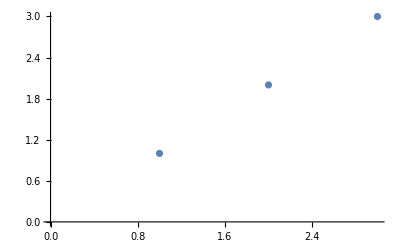

```mathematica
ListPlot[{0,-26656.657011192012,3}]
```

```mathematica
avstable = Parallelize[Table[Momentarm[Degree[angle]],{angle,10,70,10}]]
```

{°[10],°[20],°[30],°[40],°[50],°[60],°[70]}

```mathematica
ListPlot[avstable]
```

-Graphics-